```mathematica
MatrixForm[FromNormalToComplete[5]]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 3 | 1 | 0
0 | 1 | 7 | 6 | 1)

```mathematica
Join[{0},Table[Indexed[a,i],{i,1,4}]].FromNormalToComplete[5]
```

{0,a1+a2+a3+a4,a2+3 a3+7 a4,a3+6 a4,a4}

```mathematica
FromNormalToComplete[5].Join[{0},Table[Indexed[a,i],{i,1,4}]]
```

{0,a1,a1+a2,a1+3 a2+a3,a1+7 a2+6 a3+a4}

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[CompleteGraph[5],x]]
```

{0,0,0,0,0,1}

```mathematica
ChromaticPolynomial[CompleteGraph[5],x]
```

24 x-50 x^2+35 x^3-10 x^4+x^5

```mathematica
Reduce[a11+a21+a22+a23+a24+a25+a26+a27+a31+a32+a33+a34+a35+a36+a41==0]
```

a11==-a21-a22-a23-a24-a25-a26-a27-a31-a32-a33-a34-a35-a36-a41

```mathematica
MobiusM
```

MobiusM

```mathematica
Det[MobiusM]
```

Det[MobiusM]

```mathematica
MatrixPlot[MatrixPower[MobiusM,5]]
```

MatrixPlot::mat0: Argument MatrixPower[MobiusM,5] at position 1 is not a matrix.

MatrixPlot[MatrixPower[MobiusM,5]]

```mathematica
6170/24
```

3085/12

```mathematica
With[{nn=20},CoefficientList[Series[Log[1/(1+Log[1-x])],{x,0,nn}],x]Range[0,nn]!] (*Harvey P.Dale,Dec 15 2012*)
```

{0,1,2,7,35,228,1834,17582,195866,2487832,35499576,562356672,9794156448,186025364016,3826961710272,84775065603888,2011929826983504,50929108873336320,1369732445916318336,39005083331889816960,1172419218038422659456}

```mathematica
Sum_{k=1..n} (k-1)!*|Stirling1(n,k)|.-Vladeta Jovovic,Sep 14 2003
```

```mathematica
With[
{n=6},
Sum[(k-1)!*StirlingS1[n,k],{k,1,n}]
]
```

-26

```mathematica
MatrixPower[MobiusM,2]
```

MatrixPower[MobiusM,2]

```mathematica
{{1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,-35,-35,-35,-35,-35,-35,-35,-35,-35,-35,228},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7,7,7,7,7,7,0,0,0,0,-35},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,-2,0,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,7,7,7,0,0,0,7,7,7,0,-35},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,-2,0,0,0,0,0,0,0,0,0,4,4,4,0,0,0,0,0,0,7,-14},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,-2,0,-2,0,0,0,0,0,4,0,0,0,0,7,4,4,0,0,-14},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,-2,-2,0,0,0,4,0,0,4,4,0,0,0,7,0,-14},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,0,-2,0,0,0,0,0,0,-2,0,-2,0,0,0,-2,-2,0,7,0,0,7,7,0,7,7,0,7,-35},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,7,0,0,0,0,4,0,0,4,4,-14},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,-2,0,0,0,0,0,-2,-2,0,0,0,0,0,0,0,0,0,4,0,4,4,7,0,0,0,-14},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,0,0,0,0,0,0,-2,-2,0,0,0,0,0,0,4,0,4,0,4,0,7,0,0,-14},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,-2,0,0,0,-2,0,0,0,0,-2,0,0,0,0,4,0,0,7,0,4,0,4,0,-14},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,-2,0,0,0,0,0,0,4,7,0,0,0,4,4,0,-14},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,0,0,7,4,0,0,4,0,0,4,-14},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,-2,0,0,0,0,0,0,0,0,-2,0,0,7,0,0,4,0,0,4,0,4,-14},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,-2,0,0,-2,0,0,-2,0,-2,0,-2,0,7,0,7,0,7,7,0,7,7,-35},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,-2,0,0,0,-2,0,-2,0,-2,-2,0,0,7,0,7,7,0,7,7,7,-35},1,2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,0,0,0,0,0,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,-2,-2,0,0,0,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,0,0,0,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,-2,0,0,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,-2,0,-2,0,0,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,-2,-2,0,0,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,-2,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,-2,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,-2,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,-2,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,-2,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,-2,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,-2,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,-2,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,-2,0,0,0,-2,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-2,0,-2,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-2,0,0,0,-2,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-2,0,0,-2,0,0,-2,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-2,0,0,-2,0,-2,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-2,0,0,-2,-2,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
```

{{1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,-35,-35,-35,-35,-35,-35,-35,-35,-35,-35,228},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7,7,7,7,7,7,0,0,0,0,-35},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,-2,0,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,7,7,7,0,0,0,7,7,7,0,-35},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,-2,0,0,0,0,0,0,0,0,0,4,4,4,0,0,0,0,0,0,7,-14},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,-2,0,-2,0,0,0,0,0,4,0,0,0,0,7,4,4,0,0,-14},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,-2,-2,0,0,0,4,0,0,4,4,0,0,0,7,0,-14},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,0,-2,0,0,0,0,0,0,-2,0,-2,0,0,0,-2,-2,0,7,0,0,7,7,0,7,7,0,7,-35},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,7,0,0,0,0,4,0,0,4,4,-14},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,-2,0,0,0,0,0,-2,-2,0,0,0,0,0,0,0,0,0,4,0,4,4,7,0,0,0,-14},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,0,0,0,0,0,0,-2,-2,0,0,0,0,0,0,4,0,4,0,4,0,7,0,0,-14},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,-2,0,0,0,-2,0,0,0,0,-2,0,0,0,0,4,0,0,7,0,4,0,4,0,-14},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,-2,0,0,0,0,0,0,4,7,0,0,0,4,4,0,-14},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,0,0,7,4,0,0,4,0,0,4,-14},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,-2,0,0,0,0,0,0,0,0,-2,0,0,7,0,0,4,0,0,4,0,4,-14},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,-2,0,0,-2,0,0,-2,0,-2,0,-2,0,7,0,7,0,7,7,0,7,7,-35},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,-2,0,0,0,-2,0,-2,0,-2,-2,0,0,7,0,7,7,0,7,7,7,-35},1,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,-4,-4,0,0,0,0,0,0,0,14},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,-2,-2,0,0,0,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,0,0,0,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,-2,0,0,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,-2,0,-2,0,0,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,-2,-2,0,0,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,-2,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,-2,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,-2,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,-2,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,-2,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,-2,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,-2,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,-2,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,-2,0,0,0,-2,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-2,0,-2,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-2,0,0,0,-2,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-2,0,0,-2,0,0,-2,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-2,0,0,-2,0,-2,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-2,0,0,-2,-2,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Table[allGraphs5[k,"colofourrealnull"],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5,n12x3x4x5,n123x4x5,n1234x5,n12345,n1235x4,n123x45,n124x3x5,n1245x3,n124x35,n125x3x4,n125x34,n12x34x5,n12x345,n12x35x4,n12x3x45,n13x2x4x5,n134x2x5,n1345x2,n134x25,n135x2x4,n135x24,n13x24x5,n13x245,n13x25x4,n13x2x45,n14x2x3x5,n145x2x3,n145x23,n14x23x5,n14x235,n14x25x3,n14x2x35,n15x2x3x4,n15x23x4,n15x234,n15x24x3,n15x2x34,n1x23x4x5,n1x234x5,n1x2345,n1x235x4,n1x23x45,n1x24x3x5,n1x245x3,n1x24x35,n1x25x3x4,n1x25x34,n1x2x34x5,n1x2x345,n1x2x35x4,n1x2x3x45}

```mathematica
Table[allGraphs5[k,"colofourrealnull"]->allGraphs5[k,"vertexsets"],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5→{{1},{2},{3},{4},{5}},n12x3x4x5→{{1,2},{3},{4},{5}},n123x4x5→{{1,2,3},{4},{5}},n1234x5→{{1,2,3,4},{5}},n12345→{{1,2,3,4,5}},n1235x4→{{1,2,3,5},{4}},n123x45→{{1,2,3},{4,5}},n124x3x5→{{1,2,4},{3},{5}},n1245x3→{{1,2,4,5},{3}},n124x35→{{1,2,4},{3,5}},n125x3x4→{{1,2,5},{3},{4}},n125x34→{{1,2,5},{3,4}},n12x34x5→{{1,2},{3,4},{5}},n12x345→{{1,2},{3,4,5}},n12x35x4→{{1,2},{3,5},{4}},n12x3x45→{{1,2},{3},{4,5}},n13x2x4x5→{{1,3},{2},{4},{5}},n134x2x5→{{1,3,4},{2},{5}},n1345x2→{{1,3,4,5},{2}},n134x25→{{1,3,4},{2,5}},n135x2x4→{{1,3,5},{2},{4}},n135x24→{{1,3,5},{2,4}},n13x24x5→{{1,3},{2,4},{5}},n13x245→{{1,3},{2,4,5}},n13x25x4→{{1,3},{2,5},{4}},n13x2x45→{{1,3},{2},{4,5}},n14x2x3x5→{{1,4},{2},{3},{5}},n145x2x3→{{1,4,5},{2},{3}},n145x23→{{1,4,5},{2,3}},n14x23x5→{{1,4},{2,3},{5}},n14x235→{{1,4},{2,3,5}},n14x25x3→{{1,4},{2,5},{3}},n14x2x35→{{1,4},{2},{3,5}},n15x2x3x4→{{1,5},{2},{3},{4}},n15x23x4→{{1,5},{2,3},{4}},n15x234→{{1,5},{2,3,4}},n15x24x3→{{1,5},{2,4},{3}},n15x2x34→{{1,5},{2},{3,4}},n1x23x4x5→{{1},{2,3},{4},{5}},n1x234x5→{{1},{2,3,4},{5}},n1x2345→{{1},{2,3,4,5}},n1x235x4→{{1},{2,3,5},{4}},n1x23x45→{{1},{2,3},{4,5}},n1x24x3x5→{{1},{2,4},{3},{5}},n1x245x3→{{1},{2,4,5},{3}},n1x24x35→{{1},{2,4},{3,5}},n1x25x3x4→{{1},{2,5},{3},{4}},n1x25x34→{{1},{2,5},{3,4}},n1x2x34x5→{{1},{2},{3,4},{5}},n1x2x345→{{1},{2},{3,4,5}},n1x2x35x4→{{1},{2},{3,5},{4}},n1x2x3x45→{{1},{2},{3},{4,5}}}

```mathematica
IsProperSubset[small_,large_]:=Length[Intersection[small,large]]==Length[small]
```

```mathematica
IsRefinementb[sets1_,sets2_]:=Block[{sets,result=True,merged, found, set1,set2Joined},

(*each set in sets2 has to be a proper subset of a set in sets1 *)
Table[
found=False;
Table[
found= found || IsProperSubset[set2,set1]
,
{set1,sets1}
];
If[!found, result=False;Return[result]]
,
{set2,sets2}
];
result
]
```

```mathematica
RefinementVect[sets1_,sets2_]:=Block[{sets,result,merged,  set1,set2Joined,pos=1},
result=Table[0,{k,Length[sets2]}];
(*each set in sets2 has to be a proper subset of a set in sets1 *)
Table[
Table[
If[ IsProperSubset[set1,set2],
result[[pos]]++
]
,
{set1,sets1}
];
pos++
,
{set2,sets2}
];
result
]
```

```mathematica
RefinementVect[{{1},{2},{3},{4,5},{6,7},{8,9,0}},{{1,4,5,6,7},{2,8,9,0},{3}}]
```

{3,2,1}

```mathematica
ComputeValue[{{1},{2},{3},{4,5},{6,7},{8,9,0}},{{1,4,5,6,7},{2,8,9,0},{3}}]
```

ComputeValue[{{1},{2},{3},{4,5},{6,7},{8,9,0}},{{1,4,5,6,7},{2,8,9,0},{3}}]

```mathematica
ComputeValue[sets1_,sets2_]:=Block[{diff,vect},
If[IsRefinementb[sets1,sets2],
vect=RefinementVect[sets2,sets1];
Product[k,{k,Map[(-1)^(#-1)(#-1)!&,vect]}],
0
]
]
```

```mathematica
MakeIt5:=Block[{result, atoms=Table[allGraphs5[k,"vertexsets"],{k,Sort[allGraphs5NullAtomKeys]}], atomI, atomJ},
result=Monitor[
Table[
atomI=atoms[[i]];
Table[
atomJ=atoms[[j]];
If[atomI==atomJ,
1,
ComputeValue[atomI,atomJ]
]
,
{j,Length[atoms]}
],
{i,Length[atoms]}
],
{i,j}
];
result
]
```

```mathematica
MakeIt4:=Block[{result, atoms=Table[allGraphs4[k,"vertexsets"],{k,Sort[allGraphs4NullAtomKeys]}], atomI, atomJ},
result=Monitor[
Table[
atomI=atoms[[i]];
Table[
atomJ=atoms[[j]];
If[atomI==atomJ,
1,
ComputeValue[atomI,atomJ]
]
,
{j,Length[atoms]}
],
{i,Length[atoms]}
],
{i,j}
];
result
]
```

```mathematica
MakeIt[all_]:=Block[{result, atoms=Table[all[k,"vertexsets"],{k,Sort[Select[Keys[all],Length[ListofVars[all[#,"colofourrealnul"]]]==1&]]}], atomI, atomJ},
Print[Sort[Select[Keys[all],Length[ListofVars[all[#,"colofourrealnul"]]]==1&]]];
result=Monitor[
Table[
atomI=atoms[[i]];
Table[
atomJ=atoms[[j]];
If[atomI==atomJ,
1,
ComputeValue[atomI,atomJ]
]
,
{j,Length[atoms]}
],
{i,Length[atoms]}
],
{i,j}
];
result
]
```

```mathematica
MakeIt[allGraphs3]//MatrixForm
```

{0,1,2,3,4,6,9,10,12,13,14,16,18,22,26}

(1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 0 | -1 | -1 | 1 | -1 | -1 | -1 | -1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0
-1 | -1 | 0 | -1 | -1 | 1 | -1 | -1 | -1 | -1 | 0 | 1 | 0 | 0 | 0
-1 | -1 | 0 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 1 | 1 | 0
-1 | -1 | 0 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 1 | 1 | 0
2 | 2 | -1 | 2 | 2 | -1 | 2 | 2 | 2 | 2 | -1 | -1 | -1 | -1 | 1)

```mathematica
Factorial[0]
```

1

```mathematica
MatrixForm[MakeIt4,TableHeadings->{Table[allGraphs4[k,"colofourrealnull"],{k,Sort[allGraphs4NullAtomKeys]}],Map[Rotate[#,-Pi/2]&, Table[allGraphs4[k,"colofourrealnull"],{k,Sort[allGraphs4NullAtomKeys]}]]}]
```

( | n1x2x3x4 | n1x2x34 | n1x24x3 | n1x23x4 | n1x234 | n14x2x3 | n14x23 | n13x2x4 | n13x24 | n134x2 | n12x3x4 | n12x34 | n124x3 | n123x4 | n1234
n1x2x3x4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x2x34 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x24x3 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x23x4 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x234 | 2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n14x2x3 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n14x23 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n13x2x4 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n13x24 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
n134x2 | 2 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
n12x3x4 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
n12x34 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0
n124x3 | 2 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
n123x4 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0
n1234 | -6 | 2 | 2 | 2 | -1 | 2 | -1 | 2 | -1 | -1 | 2 | -1 | -1 | -1 | 1)

```mathematica
Partition
```

Partition

```mathematica
MatrixForm[MakeIt5,TableHeadings->{Table[allGraphs5[k,"colofourrealnull"],{k,Sort[allGraphs5NullAtomKeys]}],Map[Rotate[#,-Pi/2]&, Table[allGraphs5[k,"colofourrealnull"],{k,Sort[allGraphs5NullAtomKeys]}]]}]
```

( | n1x2x3x4x5 | n1x2x3x45 | n1x2x35x4 | n1x2x34x5 | n1x2x345 | n1x25x3x4 | n1x25x34 | n1x24x3x5 | n1x24x35 | n1x245x3 | n1x23x4x5 | n1x23x45 | n1x235x4 | n1x234x5 | n1x2345 | n15x2x3x4 | n15x2x34 | n15x24x3 | n15x23x4 | n15x234 | n14x2x3x5 | n14x2x35 | n14x25x3 | n14x23x5 | n14x235 | n145x2x3 | n145x23 | n13x2x4x5 | n13x2x45 | n13x25x4 | n13x24x5 | n13x245 | n135x2x4 | n135x24 | n134x2x5 | n134x25 | n1345x2 | n12x3x4x5 | n12x3x45 | n12x35x4 | n12x34x5 | n12x345 | n125x3x4 | n125x34 | n124x3x5 | n124x35 | n1245x3 | n123x4x5 | n123x45 | n1235x4 | n1234x5 | n12345
n1x2x3x4x5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x2x3x45 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x2x35x4 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x2x34x5 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x2x345 | 2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x25x3x4 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x25x34 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x24x3x5 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x24x35 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x245x3 | 2 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x23x4x5 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x23x45 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x235x4 | 2 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x234x5 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1x2345 | -6 | 2 | 2 | 2 | -1 | 2 | -1 | 2 | -1 | -1 | 2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n15x2x3x4 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n15x2x34 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n15x24x3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n15x23x4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n15x234 | -2 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n14x2x3x5 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n14x2x35 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n14x25x3 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n14x23x5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n14x235 | -2 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n145x2x3 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n145x23 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n13x2x4x5 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n13x2x45 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n13x25x4 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n13x24x5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n13x245 | -2 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n135x2x4 | 2 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n135x24 | -2 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n134x2x5 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n134x25 | -2 | 0 | 0 | 1 | 0 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1345x2 | -6 | 2 | 2 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | -1 | 0 | 2 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n12x3x4x5 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n12x3x45 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n12x35x4 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n12x34x5 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n12x345 | -2 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n125x3x4 | 2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n125x34 | -2 | 0 | 0 | 2 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n124x3x5 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n124x35 | -2 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
n1245x3 | -6 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
n123x4x5 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
n123x45 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0
n1235x4 | -6 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
n1234x5 | -6 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0
n12345 | 24 | -6 | -6 | -6 | 2 | -6 | 2 | -6 | 2 | 2 | -6 | 2 | 2 | 2 | -1 | -6 | 2 | 2 | 2 | -1 | -6 | 2 | 2 | 2 | -1 | 2 | -1 | -6 | 2 | 2 | 2 | -1 | 2 | -1 | 2 | -1 | -1 | -6 | 2 | 2 | 2 | -1 | 2 | -1 | 2 | -1 | -1 | 2 | -1 | -1 | -1 | 1)

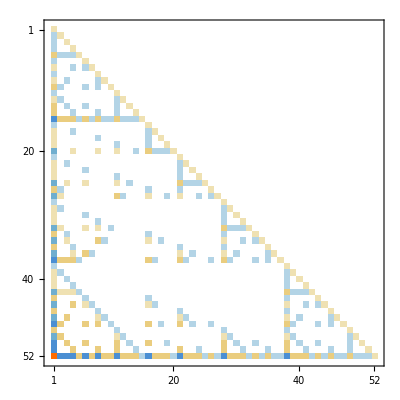

```mathematica
MakeIt5//MatrixPlot
```

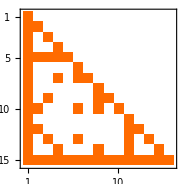

```mathematica
MatrixPower[Inverse[MakeIt4],1]//MatrixPlot
```

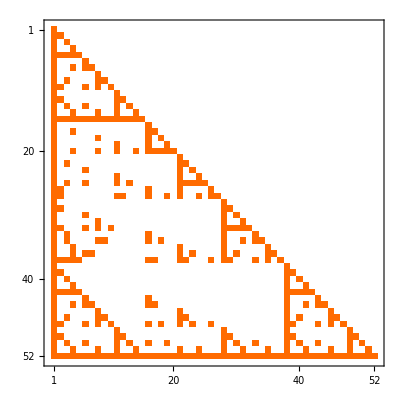

```mathematica
MatrixPower[Inverse[MakeIt5],1]//MatrixPlot
```

```mathematica
Map[Total,MakeIt4]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

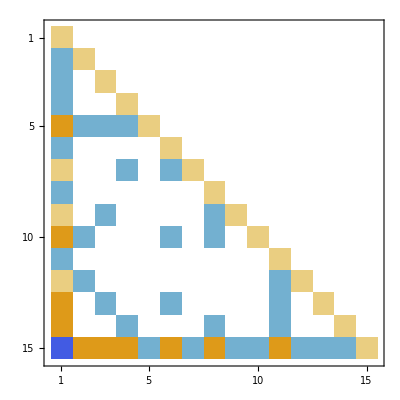

```mathematica
MakeIt4//MatrixPlot
```

```mathematica
Sort[Tally[Flatten[MakeIt5]]]
```

{{-6,15},{-2,10},{-1,160},{0,2346},{1,97},{2,75},{24,1}}

```mathematica
Sort[Tally[Flatten[MakeIt5]]]
```

{{-6,15},{-2,10},{-1,160},{0,2346},{1,97},{2,75},{24,1}}

```mathematica
Sort[Tally[Flatten[MobiusM]]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[MobiusM].

Tally::list: List expected at position 1 in Tally[Flatten[MobiusM]].

Tally[Flatten[MobiusM]]